```mathematica
Off[SixJSymbol::tri];
Off[ThreeJSymbol::tri];
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
$Assumptions=α∈Reals;
```

```mathematica
(* The total angular momentum quantum number is conserved, so we solve only for a specific J0 *)
J0=0;
(* The full two-body energy cutoff for the basis *)
EMax=25;(*=NMax+3*)
(* Easiest to set a value of a at the beginning so that the matrix elements become numerical *)
a=1;
(* This is needed because the eigensolver finds the eigenvalues with the smallest magnitude. Choose a postive number at least the size of the most negative eigenvalue expected *)
EOffset=20;
```

```mathematica
(* Determine the two body l=0 center of mass eigenenergies in the absence of SOC from Busch formula *)
If[a!=0,
νValues=Table[FindRoot[Sqrt[2]Gamma[-ν]/Gamma[-ν-1/2]==1/a,{ν,νGuess},AccuracyGoal->25],{νGuess,-2,(EMax/2-.75)+.25,.05*Sqrt[2]}];
νValues=DeleteDuplicates[νValues,Abs[ReplaceAll[ν,#1]-ReplaceAll[ν,#2]]<=.1&];,
νValues=Table[{ν->i},{i,0,EMax-3}] (* Handle a=0 case *);]

EValues=Sort[2ν+3/2/.νValues] ;(* List of l=0 energies under the cutoff *)
νValues=Sort[Flatten[ν/.νValues]];
```

```mathematica
(* List of Busch quantum numbers under the energy cutoff *)
νValues
```

{-1.19964,0.310307,1.35611,2.37913,3.39367,4.40394,5.4117,6.41783,7.42283,8.42702,9.43059,10.4337,11.4364}

```mathematica
(* List of Busch 2-body Relative Energies below the cutoff *)
EValues
```

{-0.899286,2.12061,4.21222,6.25825,8.28734,10.3079,12.3234,14.3357,16.3457,18.354,20.3612,22.3674,24.3728}

```mathematica
(* Indexing of states *)
Clear[ni,li,Ni,Li,si,ji,Ji];
imax=0;
i=0;
verbose=False;

If[EValues[[1]]≤3/2,δEMax=EValues[[1]]-3/2,δEMax=0];

(* Function to print quantum numbers of state i if needed *)
PrintState[i_]:=Print["|",i,">=|",ni[i],"(",li[i],si[i],")",ji[i],";",Ni[i],Li[i],";(",ji[i],Li[i],")",Ji[i],">"];

For[EShell=3,EShell≤EMax,++EShell,
For[N0=0,2 N0+3+δEMax≤EShell,++N0,
For[L=0,2 N0+L+3+δEMax≤EShell,++L,
For[s=0,s≤1,++s,
For[j=Max[J0-L,0],j-L≤J0,++j,
For[l=0,l<=Max[EShell-2N0-L-3/2-EValues[[1]],EShell-2N0-L-3],++l,
If[l==0&&s==0,
For[ii=1,2N0+L+3/2+EValues[[ii]]≤EShell&&ii≤Length[EValues],++ii,
If[(EShell-1<2N0+L+3/2+EValues[[ii]]||EShell==3)&&2N0+L+3/2+EValues[[ii]]≤EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;
Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=νValues[[ii]];
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2*ni[i]+3/2];](* End If[Verbose] *)
](* End If[EvenQ... ] *)
] (* End ii loop *)(* End l==0 case, ν loop*),
For[n=0,2n+l+3/2+2N0+L+3/2≤EShell,++n,
If[EvenQ[l+s]&&2(N0+n)+L+l+3==EShell&&Abs[l-s]≤j≤l+s&&Abs[L-j]≤J0≤Abs[L+j],
++i;++imax;

Ji[i]=J0;
Ni[i]=N0;
Li[i]=L;
si[i]=s;
li[i]=l;
ji[i]=j;
ni[i]=n;
If[verbose,
Print["E_shell=",EShell,"   |",i,">=|",ni[i],"(",l,s,")",j,";",N0,L,";(",j,L,")",J0,">"];
Print["E=",2N0+L+3/2+2ni[i]+l+3/2];](* End If[Verbose] *)
] (* End If[EvenQ...] *)
](* End For[n=0...] *)
] (* End If[l==0] *)
](* End l loop *)
] (* End j loop *)
] (* End s loop *)
] (* End L loop *)
];(* End N0 loop *)
iShell[EShell]=imax;
] (* End EShell loop *)
Clear[i,ii,l,L,N0,n,s,j];
Print["There are a total of ",imax," ","included states."]
```

There are a total of 651 included states.

```mathematica
shellSizeTableWeyl = 
 Table[{EShell, iShell[EShell]}, {EShell, 4, Min[32, EMax]}];
ListPlot[shellSizeTableWeyl,Joined->True,PlotRange->{{0,Min[32,EMax]},{0,2000}},Axes->False,Frame->True,PlotLabel->"Number of J=0, Jz=0 states with E<=E_Max",FrameLabel->{"E_Max","Number of States"}];
```

```mathematica
(* Save all the angular momentum coupling coefficients after computing once *)
JThree[{j1_,j1m_},{j2_,j2m_},{J_,Jm_}]:=JThree[{j1,j1m},{j2,j2m},{J,Jm}]=ThreeJSymbol[{j1,j1m},{j2,j2m},{J,Jm}];
JSix[{j1_,j2_,j3_},{j4_,j5_,j6_}]:=JSix[{j1,j2,j3},{j4,j5,j6}]=SixJSymbol[{j1,j2,j3},{j4,j5,j6}];
```

```mathematica
(* Normalization factor for Busch wave functions. Provide a limiting definition for half-integer ν when a->+∞,-∞ *)
Clear[A];
AbsoluteTiming[If[a≠∞&&a≠-∞,A[ν_]:=A[ν]=((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),
For[ν0=-1/2,ν0<=νValues[[-1]]+.01,ν0++,A[N[ν0]]=Limit[((Gamma[-ν] (-PolyGamma[0,-1/2-ν]+PolyGamma[0,-ν]))/(8 π^2 Gamma[-1/2-ν]))^(-1/2),ν->ν0]]
] (* End if *)
] (* End AbsoluteTiming *)
```

{0.00005,Null}

```mathematica
(* This is the actual reduced matrix element of Q *)
Q[n1_,l1_,n_,l_]:=If[Abs[l1-l]==1,(I (-1)^(l1+1))/JThree[{l1,0},{1,0},{l,0}] √(n!n1!Gamma[n+l+3/2]Gamma[n1+l1+3/2])Sum[(-1)^(m+m1)/(m!m1!(n-m)!(n1-m1)!Gamma[m+l+3/2]Gamma[m1+l1+3/2])Which[l1==l+1,(l+1)/Sqrt[(2l+1)(2l+3)] (2m Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),l1==l-1,l/Sqrt[(2l+1)(2l-1)]((2m+2l+1) Gamma[m+m1+1+(l+l1)/2]-Gamma[m+m1+2+(l+l1)/2]),True,0],{m,0,n},{m1,0,n1}],0];
(* This is the actual reduced matrix element of q, accounting for the Busch states at l=0 *)
q[n1_,l1_,n_,l_]:=
If [l1>0&&l>0||a==0,(* Case where neither l or l1=0, or when there is no two-body interaction *)Q[n1,l1,n,l],
If[l1==0&&l==1&&a≠0,(* Recursive definition for < ν l1=0 ||q || n l=1 > case *)q[n,1,n1,0], 
If[l1==1&&l==0&&a≠0, (* Definition for < n1 l1=1 ||q || ν l=0 > case *)
-I A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))
]
]
];
```

```mathematica
(* Matrix elements of σ.q *)
(* Remember to multiply by the 1/Sqrt[2] term from changing coordinates, and the Sqrt[3] term from the difference between a dot product and a tensor scalar product *)(*σq[n1_,s1_,l1_,n_,s_,l_,j_]:=  Sqrt[6](-1)^(l+s1+j)JSix[{j,s1,l1},{1,l,s}](s1-s)q[n1,l1,n,l];*)
σq[n1_,s1_,l1_,n_,s_,l_,j_]:=Sqrt[3]/Sqrt[2] 2/Sqrt[2j+1](-1)^(l+s1+j)(s1-s)q[n1,l1,n,l];
```

```mathematica
(* Matrix elements of Σ.Q *)
ΣQ[N1_,l1_,j1_,L1_,N_,l_,s_,j_,L_,J_]:=Sqrt[3]/Sqrt[2] 2Sqrt[6(2j1+1)(2j+1)](-1)^(L1+1)Q[N1,L1,N,L]Sum[(-1)^J2(2J2+1)JSix[{l,1,j1},{L1,J,J2}]JSix[{l,1,j},{L,J,J2}]JSix[{J2,1,L1},{1,L,1}],{J2,Abs[L-s],Abs[L+s]}]
```

```mathematica
(* Matrix σ.q+Σ.Q, stored as SparseArray *)
Print["There are a total of ",imax," ","included states."]
t=AbsoluteTime[];
σqΣQ=SparseArray[
Flatten[
ParallelTable[Quiet[If[Ji[i]==Ji[j],
If[Ni[i]==Ni[j]&&Li[i]==Li[j]&&ji[i]==ji[j]&&Abs[li[i]-li[j]]==1,{{i,j}->σq[ni[i],si[i],li[i],ni[j],si[j],li[j],ji[j]]},(*ELSE*)If[ni[i]==ni[j]&&li[i]==li[j]&&si[i]==1&&si[j]==1&&Abs[Li[i]-Li[j]]==1,{{i,j}->Chop[ΣQ[Ni[i],li[i],ji[i],Li[i],Ni[j],li[j],si[j],ji[j],Li[j],Ji[j]]]},##&[]]
,##&[]](* If σq≠0 *)
,##&[]](* If j≤i && J==J *)
](* End quiet *)
(* TEST ,{i,2,imax},{j,1,i-1}]*)
,{i,2,imax},{j,1,i-1}]
],{imax,imax}
];
σqΣQ=SparseArray[σqΣQ+ConjugateTranspose[σqΣQ]];
AbsoluteTime[]-t
```

There are a total of 3803 included states.

219.88608

```mathematica
(* Matrix of Subscript[H, HO]+Subscript[H, contact], stored as SparseArray *)
H0=SparseArray[ParallelTable[{i,i}->2ni[i]+2Ni[i]+li[i]+Li[i]+3+EOffset,{i,1,imax}]];
```

```mathematica
αTest=.5;
Eigensystem[H0+αTest σqΣQ,-8][[1,-1]]-EOffset
GS=Eigensystem[H0+αTest σqΣQ,-8][[2,-1]];
Abs[GS[[1]]]
Ordering[Abs[GS],-20]
Map[PrintState,%]
```

-15.0165

0.99258

{2480,2119,11,1795,1506,1250,1025,829,660,516,15,395,295,214,24,150,101,40,65,1}

|2480>=|18(11)0;00;(00)0>

|2119>=|17(11)0;00;(00)0>

|11>=|0(11)0;00;(00)0>

|1795>=|16(11)0;00;(00)0>

|1506>=|15(11)0;00;(00)0>

|1250>=|14(11)0;00;(00)0>

|1025>=|13(11)0;00;(00)0>

|829>=|12(11)0;00;(00)0>

|660>=|11(11)0;00;(00)0>

|516>=|10(11)0;00;(00)0>

|15>=|1(11)0;00;(00)0>

|395>=|9(11)0;00;(00)0>

|295>=|8(11)0;00;(00)0>

|214>=|7(11)0;00;(00)0>

|24>=|2(11)0;00;(00)0>

|150>=|6(11)0;00;(00)0>

|101>=|5(11)0;00;(00)0>

|40>=|3(11)0;00;(00)0>

|65>=|4(11)0;00;(00)0>

|1>=|-8.7461(00)0;00;(00)0>

{Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null,Null}

```mathematica
Abs[Eigensystem[H0+.25 σqΣQ,-8][[2,-1]]][[19]]
```

4.23576×10^-18

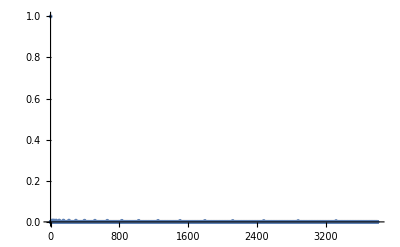

```mathematica
ListPlot[Abs[GS],PlotRange->All]
```

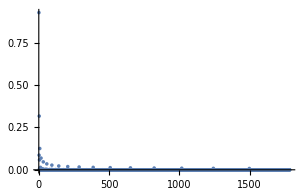
```mathematica
(* a=∞ *)
-Graphics-
```

-Graphics-

```mathematica
MemoryInUse[]/10^6//N
MaxMemoryUsed[]/10^6//N
```

408.189

429.647

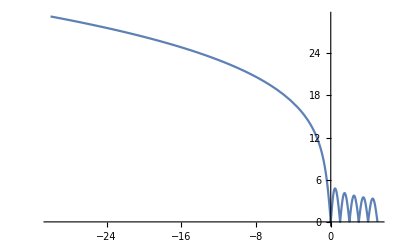

```mathematica
Plot[A[ν],{ν,-30,5}]
```

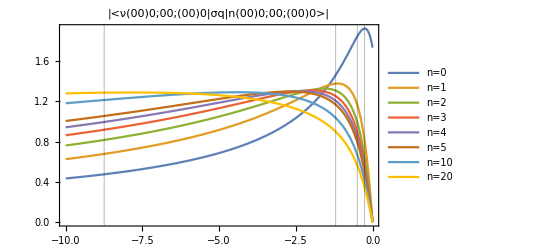

```mathematica
nmax=5;
MatrixElts=Table[Abs[Sqrt[3]/Sqrt[2] 2/Sqrt[3] A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))],{n1,0,nmax}];
AppendTo[MatrixElts,ReplaceAll[Abs[Sqrt[3]/Sqrt[2] 2/Sqrt[3] A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))],n1->10]];
AppendTo[MatrixElts,ReplaceAll[Abs[Sqrt[3]/Sqrt[2] 2/Sqrt[3] A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n))],n1->20]];
Fig=Plot[MatrixElts,{n,-10,0},PlotStyle->Automatic,Axes->False,Frame->True,PlotLabel->"|<ν(00)0;00;(00)0|σq|n(00)0;00;(00)0>|",PlotLegends->Join[Table[StringJoin["n=",ToString[n2]],{n2,0,nmax}],{"n=10","n=20"}],GridLines->{{{-1.1996432225271036(*a=1*),Black},{-0.2562988229195664(*a=-1*),Black},{-8.746100370356269(*a=.25*),Black},{-0.5 (*a=∞*),Black}},{}}]
Export["/Users/cdschillaci/Desktop/Paper with Tom/Mathematica/Figures/sig_dot_q_mat_elts.eps",Fig]
```

```mathematica
Abs[MatrixElts/.n->-.2]
```

{1.91483,0.668433,0.526651,0.462999,0.424399,0.39754}

```mathematica
Table[A[n]Sqrt[Gamma[n1+5/2]/(2 π^3 Gamma[n1+1])](-1-2 n1+2 n)/(2 (n1-n) (1+n1-n)),{n1,0,4}]
```

{-(√3 (-1+2 n))/(2 (1-n) n π^(1/4) √((Gamma[-n] (-PolyGamma[0,-1/2-n]+PolyGamma[0,-n]))/Gamma[-1/2-n])),(√(15/2) (-3+2 n))/(2 (1-n) (2-n) π^(1/4) √((Gamma[-n] (-PolyGamma[0,-1/2-n]+PolyGamma[0,-n]))/Gamma[-1/2-n])),(√(105/2) (-5+2 n))/(4 (2-n) (3-n) π^(1/4) √((Gamma[-n] (-PolyGamma[0,-1/2-n]+PolyGamma[0,-n]))/Gamma[-1/2-n])),(3 √35 (-7+2 n))/(8 (3-n) (4-n) π^(1/4) √((Gamma[-n] (-PolyGamma[0,-1/2-n]+PolyGamma[0,-n]))/Gamma[-1/2-n])),(3 √(385/2) (-9+2 n))/(16 (4-n) (5-n) π^(1/4) √((Gamma[-n] (-PolyGamma[0,-1/2-n]+PolyGamma[0,-n]))/Gamma[-1/2-n]))}

```mathematica
Join[Flatten[Table[StringJoin["n=",ToString[n2]],{n2,0,nmax}]],{"n=10","n=20"}]
```

{n=0,n=1,n=2,n=3,n=4,n=5,n=10,n=20}